```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
P[s_,β_]:=(1+β)Gamma[(β+2)/(β+1)]^(β+1)s^β Exp[-Gamma[(β+2)/(β+1)]^(β+1)s^(β+1)];
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2;
```

```mathematica
Sigma[data_List,l_]:=N[(Length[data]-1)/Length[data] Variance[BinCounts[data,Append[{-l,l}+MinMax[data],l]]]]
```

```mathematica
cliprange[points_List,xmax_]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

## Random network

```mathematica
n1=2000;p1=0.01;
gs1=RandomGraph[BernoulliGraphDistribution[n1,p1],10];
lambda1[g_Graph]:=Module[{degrees},degrees=VertexDegree[g];Eigenvalues[IdentityMatrix[n1]-(AdjacencyMatrix[g]/Sqrt[Outer[Times,N[degrees],N[degrees]]])]]
LaunchKernels[4];
DistributeDefinitions[lambda1];
alleigens1=Flatten[eigens1=ParallelMap[lambda1[#]&,gs1]];
cumuhistdata1=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[alleigens1,100,"CDF"]];
m1=15;Nbar1[x_]=Fit[cumuhistdata1,{1,Sequence@@Table[x^i,{i,1,m1}]},x];
nnd1=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Flatten[Abs[Differences/@(n1 Nbar1[#]&/@Sort[#]&/@eigens1)]],200,"PDF"]];
nnd1=cliprange[nnd1,4];
nlmNND1=NonlinearModelFit[Select[nnd1,#[[1]]≥0&],P[s,β],{β},s];
beta1=N[nlmNND1["BestFitParameters"][[1,2]]];
unfoldlamb1=Sort[(n1 Nbar1[#]&/@eigens1)];
nv1=Table[{l,Mean[Sigma[#,l]&/@unfoldlamb1]},{l,0.1,20,0.2}];
nlmNV1=NonlinearModelFit[nv1,NV[L,ξb,f],{ξb,f},L];
f1=N[nlmNV1["BestFitParameters"][[2,2]]];
xi1=N[nlmNV1["BestFitParameters"][[1,2]]];
```

## Scale free network

```mathematica
n2=2000;k2=20;
gs2=RandomGraph[BarabasiAlbertGraphDistribution[n2,k2],10];
lambda2[g_Graph]:=Module[{degrees},degrees=VertexDegree[g];Eigenvalues[IdentityMatrix[n2]-(AdjacencyMatrix[g]/Sqrt[Outer[Times,N[degrees],N[degrees]]])]]
LaunchKernels[4];
DistributeDefinitions[lambda2];
alleigens2=Flatten[eigens2=ParallelMap[lambda2[#]&,gs2]];
cumuhistdata2=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[alleigens2,100,"CDF"]];
m2=15;Nbar2[x_]=Fit[cumuhistdata2,{1,Sequence@@Table[x^i,{i,1,m2}]},x];
nnd2=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Flatten[Abs[Differences/@(n2 Nbar2[#]&/@Sort[#]&/@eigens2)]],200,"PDF"]];
nnd2=cliprange[nnd2,4];
nlmNND2=NonlinearModelFit[Select[nnd2,#[[1]]≥0&],P[s,β],{β},s];
beta2=N[nlmNND2["BestFitParameters"][[1,2]]];
unfoldlamb2=Sort[(n2 Nbar2[#]&/@eigens2)];
nv2=Table[{l,Mean[Sigma[#,l]&/@unfoldlamb2]},{l,0.1,20,0.2}];
nlmNV2=NonlinearModelFit[nv2,NV[L,ξb,f],{ξb,f},L];
f2=N[nlmNV2["BestFitParameters"][[2,2]]];
xi2=N[nlmNV2["BestFitParameters"][[1,2]]];
```

## Small world network

```mathematica
n3=2000;p3=0.7;k3=40;
gs3=RandomGraph[WattsStrogatzGraphDistribution[n3,p3,k3],10];
lambda3[g_Graph]:=Module[{degrees},degrees=VertexDegree[g];Eigenvalues[IdentityMatrix[n3]-(AdjacencyMatrix[g]/Sqrt[Outer[Times,N[degrees],N[degrees]]])]]
LaunchKernels[4];
DistributeDefinitions[lambda3];
alleigens3=Flatten[eigens3=ParallelMap[lambda3[#]&,gs3]];
cumuhistdata3=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[alleigens3,100,"CDF"]];
m3=15;Nbar3[x_]=Fit[cumuhistdata3,{1,Sequence@@Table[x^i,{i,1,m3}]},x];
nnd3=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Flatten[Abs[Differences/@(n3 Nbar3[#]&/@Sort[#]&/@eigens3)]],200,"PDF"]];
nnd3=cliprange[nnd3,4];
nlmNND3=NonlinearModelFit[Select[nnd3,#[[1]]≥0&],P[s,β],{β},s];
beta3=N[nlmNND3["BestFitParameters"][[1,2]]];
unfoldlamb3=Sort[(n3 Nbar3[#]&/@eigens3)];
nv3=Table[{l,Mean[Sigma[#,l]&/@unfoldlamb3]},{l,0.1,20,0.2}];
nlmNV3=NonlinearModelFit[nv3,NV[L,ξb,f],{ξb,f},L];
f3=N[nlmNV3["BestFitParameters"][[2,2]]];
xi3=N[nlmNV3["BestFitParameters"][[1,2]]];
```

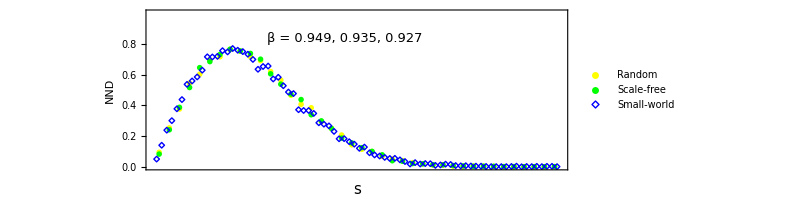

```mathematica
nndpoints=ListPlot[{nnd1,nnd2,nnd3}(*use your data*),PlotRange->{{0,4},{0,1}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->{Style["*",Orange,Thick],Style["◻",Green,Thick],Style["◇",Blue,Thick]},Frame->True,PlotStyle->{Yellow, Green, Blue},
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False],(*down*)
LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times New Roman",15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,10,FontFamily->"Times New Roman"]&/@{"Random","Scale-free","Small-world"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["  β = 0.949, 0.935, 0.927",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.47,0.82}]],Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
clippoints = Table[{s,Normal[nlmNND1]},{s,0.0001,4,0.04}] ;
nndmat=ListStepPlot[clippoints,Center,AxesOrigin->{0,0},PlotRange->{{0,4},{0,1}},PlotStyle->Lighter[Black],Frame->True];
```

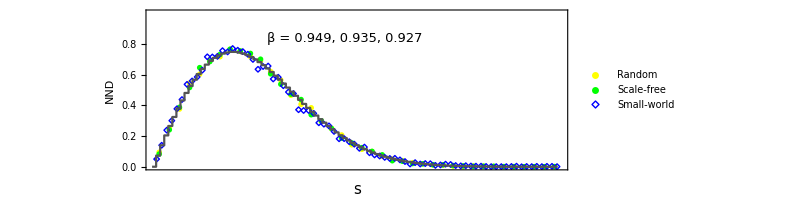

```mathematica
p1=Show[nndpoints,nndmat]
```

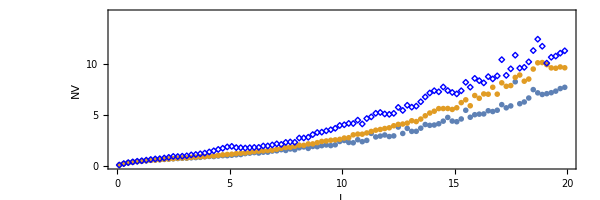

```mathematica
nvpoints=ListPlot[{nv1,nv2,nv3}(*use your data*),PlotRange->{{0,20},{0,15}},DataRange->{{0,20},{0,15}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->{Style["*",Orange,Thick],Style["◻",Green,Thick],Style["◇",Blue,Thick]},Frame->True,
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,15,5],Range[2.5,12.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,15,5],Range[2.5,12.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,20,5],Range[2.5,17.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,20,5],Range[2.5,17.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Style["NV",FontFamily->"Times New Roman",15]}]
```

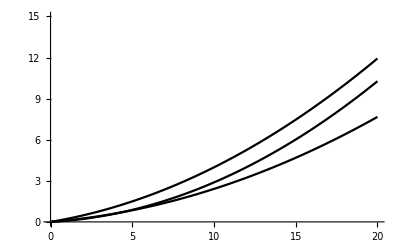

```mathematica
nvcurv=Plot[{Normal[nlmNV1],Normal[nlmNV2],Normal[nlmNV3]},{L,0,20},PlotStyle->Black,PlotRange->{{0,20},{0,15}}]
```

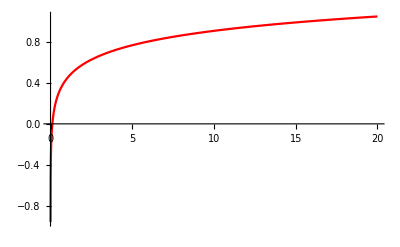

```mathematica
nvcurvGOE=Plot[2/π^2(Log[2π l]+1+EulerGamma-π^2/8),{l,0.001,20},PlotStyle->Red,PlotRange->All]
```

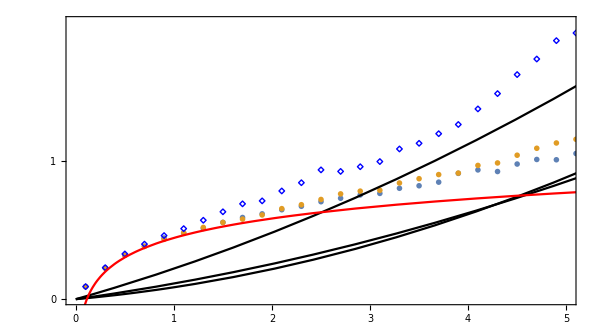

```mathematica
pinset=Show[nvpoints,nvcurv,nvcurvGOE,PlotRange->{{0,5},{0,2.}},FrameLabel->None,AspectRatio->1/1.8,ImagePadding->ip,FrameTicksStyle->Directive[thick,"Label", 8],FrameTicks->{{LinTicks[Range[0,2,1],Range[0.5,1.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,2,1],Range[0.5,1.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,5,1],Range[0.5,4.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,5,1],Range[0.5,4.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}}(*up*)]
```

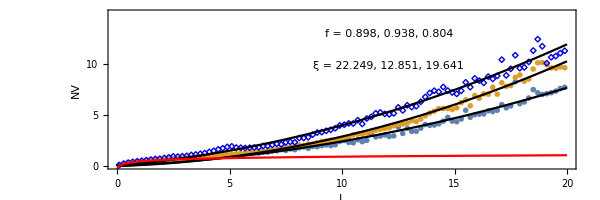

```mathematica
p2=Show[nvpoints,nvcurv,nvcurvGOE,(*we want nvcurv as background*)Epilog->{Text[Style["StyleBox[\"f\",FontSlant->\"Italic\"] = 0.898, 0.938, 0.804",FontSize->11,FontFamily->"Times New Roman"],Scaled[{0.6,0.85}]],Text[Style["\!\(\*OverscriptBox[\(ξ\), \(_\)]\) = 22.249, 12.851, 19.641",FontSize->11,FontFamily->"Times New Roman"],Scaled[{0.6,0.65}]],Inset[pinset,{0.5,4.5},{0,0},Scaled[1.12]]}]
```

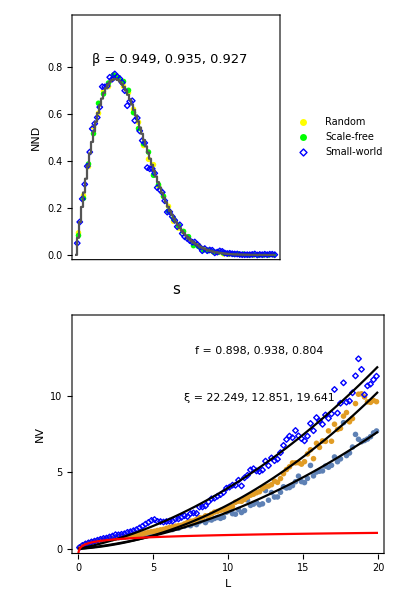

```mathematica
p=Column[{p1,p2},Spacings->-3.5]
```

```mathematica
Export["RSS_net.eps",p]
```

RSS_net.eps